```mathematica
8 7
```

56

```mathematica
Entity["Country","Netherlands"]
```

Netherlands

```mathematica
Entity["Country","Netherlands"]["Dataset"]
```

Dataset[<>]

```mathematica
DeleteMissing@Entity["Country","Netherlands"]["Dataset"]
```

Dataset[<>]

```mathematica
CountryData["Germany","ExportValue"]
```

1.59439×10^12 $

```mathematica
PercentForm@(CountryData["Germany","ExportValue"]/CountryData["Germany","GDP"])
```

45.84%

```mathematica
CountryData["UnitedStates","SectorLaborFractions"]
```

{Agriculture→0.006,Industry→0.226,Services→0.768}

```mathematica
CountryData["China","SectorLaborFractions"]
```

{Agriculture→0.43,Industry→0.25,Services→0.32}

```mathematica
DeleteMissing@Entity["Country","China"]
```

DeleteMissing::invrp: The argument China is not a valid Association or a list.

DeleteMissing[China]

```mathematica
DeleteMissing@Entity["Country","China"]["Dataset"]
```

Dataset[<>]

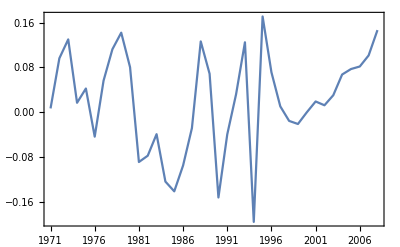

```mathematica
DateListPlot@CountryData["China",{"InflationRate",All}]
```

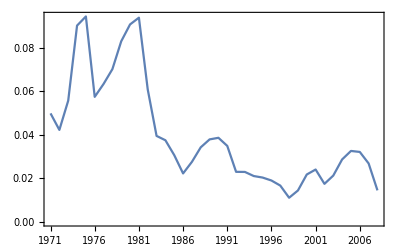

```mathematica
DateListPlot@CountryData["UnitedStates",{"InflationRate",All}]
```

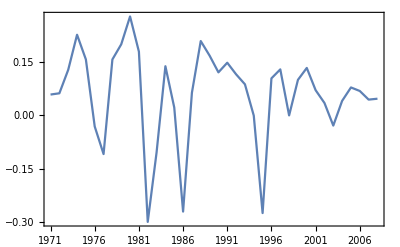

```mathematica
DateListPlot@CountryData["Mexico",{"InflationRate",All}]
```

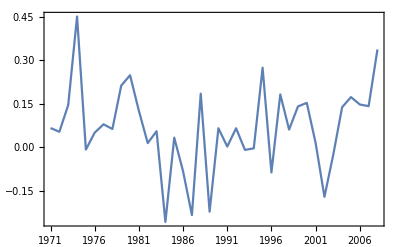

```mathematica
DateListPlot@CountryData["Venezuela",{"InflationRate",All}]
```

```mathematica
CountryData["Brazil","MerchantShips"]
```

136

```mathematica
CountryData["Brazil","MerchantShipsGross"]
```

1.99825×10^6 RT

```mathematica
CountryData["Brazil","MerchantShipTypes"]
```

{BulkCarrier→19,Cargo→22,Carrier→1,ChemicalTanker→7,Container→11,LiquefiedGas→12,PassengerCargo→12,PetroleumTanker→45,RollOnRollOff→7}

```mathematica
Grid@
TakeLargestBy[
ParallelTable[
{c,CountryData[c,"SectorLaborFractions"]},
{c,CountryData[]}]
,Last,15]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

$Aborted[]

```mathematica
Grid@
TakeLargestBy[
ParallelTable[
{c,Last@Select[CountryData[c,"SectorLaborFractions"],First@#=="Services"&]},
{c,CountryData[]}]
,Last,15]
```

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

Last::nolast: Missing[] has zero length and no last element.

Last::nolast: {} has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Last::nolast: Missing[] has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

General::stop: Further output of First::normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of Last::nolast will be suppressed during this calculation.

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::nolast: Missing[] has zero length and no last element.

Last::nolast: {} has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of Last::nolast will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Last::nolast: Missing[] has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: {} has zero length and no last element.

General::stop: Further output of First::normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

$Aborted

```mathematica
Grid@
TakeLargestBy[
Table[
{c,Last@Last@Select[CountryData[c,"SectorLaborFractions"],First@#=="Services"&]},
{c,CountryData[]}]
,Last,15]
```

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

Last::nolast: {} has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of First::normal will be suppressed during this calculation.

TakeLargestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeLargestBy[{{Afghanistan,0.1},{Aland Islands,Missing[]},{Albania,0.27},{Algeria,0.626},{American Samoa,0.33},{Andorra,0.789},{Angola,{}},{Anguilla,0.75},{Antigua and Barbuda,0.82},{Argentina,0.76},{Armenia,0.382},{Aruba,Missing[]},{Australia,0.75},{Austria,0.67},{Azerbaijan,0.486},{Bahamas,0.9},{Bahrain,0.2},{Bangladesh,0.26},{Barbados,0.75},{Belarus,0.513},{Belgium,0.73},{Belize,0.717},{Benin,Missing[]},{Bermuda,0.8},{Bhutan,0.31},{Bolivia,0.43},{Caribbean Netherlands,Missing[]},{Bosnia and Herzegovina,0.476},{Botswana,Missing[]},{Bouvet Island,Missing[]},{Brazil,0.66},{British Indian Ocean Territory,Missing[]},{British Virgin Islands,0.594},{Brunei,0.324},{Bulgaria,0.57},{Burkina Faso,{}},{Burundi,0.041},{Cambodia,{}},{Cameroon,0.17},{Canada,0.79},{Cape Verde,Missing[]},{Cayman Islands,0.86},{Central African Republic,Missing[]},{Chad,{}},{Chile,0.638},{China,0.32},{Christmas Island,Missing[]},{Cocos Keeling Islands,Missing[]},{Colombia,0.588},{Comoros,{}},{Cook Islands,0.56},{Costa Rica,0.64},{Croatia,0.637},{Cuba,0.606},{Curacao,Missing[]},{Cyprus,0.71},{Czech Republic,0.562},{Democratic Republic of the Congo,Missing[]},{Denmark,0.73},{Djibouti,Missing[]},{Dominica,0.28},{Dominican Republic,0.631},{East Timor,{}},{Ecuador,0.705},{Egypt,0.51},{El Salvador,0.58},{Equatorial Guinea,Missing[]},{Eritrea,{}},{Estonia,0.616},{Ethiopia,0.132},{Falkland Islands,{}},{Faroe Islands,0.669},{Fiji,{}},{Finland,0.699},{France,0.719},{French Guiana,0.606},{French Polynesia,0.68},{French Southern And Antarctic lands,Missing[]},{Gabon,0.25},{Gambia,0.06},{Gaza Strip,0.83},{Georgia,0.355},{Germany,0.679},{Ghana,0.29},{Gibraltar,0.6},{Greece,0.652},{Greenland,Missing[]},{Grenada,0.62},{Guadeloupe,0.65},{Guam,0.64},{Guatemala,0.35},{Guernsey,Missing[]},{Guinea,{}},{Guinea-Bissau,{}},{Guyana,Missing[]},{Haiti,0.25},{Honduras,0.399},{Hong Kong,0.92},{Hungary,0.626},{Iceland,0.78},{India,0.28},{Indonesia,0.393},{Iran,0.446},{Iraq,Missing[]},{Ireland,0.67},{Isle of Man,0.76},{Israel,0.82},{Italy,0.651},{Ivory Coast,{}},{Jamaica,0.64},{Japan,0.673},{Jersey,Missing[]},{Jordan,0.773},{Kazakhstan,0.5},{Kenya,{}},{Kiribati,0.653},{Kosovo,Missing[]},{Kuwait,Missing[]},{Kyrgyzstan,0.395},{Laos,{}},{Latvia,0.62},{Lebanon,Missing[]},{Lesotho,{}},{Liberia,0.22},{Libya,0.6},{Liechtenstein,0.549},{Lithuania,0.569},{Luxembourg,0.806},{Macau,0.799},{North Macedonia,0.5},{Madagascar,Missing[]},{Malawi,{}},{Malaysia,0.51},{Maldives,0.6},{Mali,{}},{Malta,0.68},{Marshall Islands,0.577},{Martinique,0.73},{Mauritania,0.4},{Mauritius,0.61},{Mayotte,Missing[]},{Mexico,0.59},{Micronesia,0.647},{Moldova,0.434},{Monaco,Missing[]},{Mongolia,0.61},{Montenegro,0.68},{Montserrat,Missing[]},{Morocco,0.355},{Mozambique,0.13},{Myanmar,0.23},{Namibia,0.33},{Nauru,Missing[]},{Nepal,0.18},{Netherlands,0.8},{New Caledonia,0.6},{New Zealand,0.74},{Nicaragua,0.52},{Niger,0.04},{Nigeria,0.2},{Niue,Missing[]},{Norfolk Island,{}},{Northern Mariana Islands,Missing[]},{North Korea,{}},{Norway,0.76},{Oman,Missing[]},{Pakistan,0.367},{Palau,{}},{Panama,0.67},{Papua New Guinea,{}},{Paraguay,0.52},{Peru,0.755},{Philippines,0.5},{Pitcairn Islands,Missing[]},{Poland,0.534},{Portugal,0.6},{Puerto Rico,0.79},{Qatar,Missing[]},{Republic of the Congo,Missing[]},{Réunion,0.75},{Romania,0.471},{Russia,0.624},{Rwanda,{}},{Saint Barthelemy,Missing[]},{Saint Helena, Ascension and Tristan da Cunha,0.46},{Saint Kitts and Nevis,Missing[]},{Saint Lucia,0.536},{Saint Martin,Missing[]},{Saint Pierre and Miquelon,0.41},{Saint Vincent and the Grenadines,0.57},{Samoa,Missing[]},{San Marino,0.622},{São Tomé and Príncipe,Missing[]},{Saudi Arabia,0.719},{Senegal,{}},{Serbia,0.24},{Seychelles,0.74},{Sierra Leone,Missing[]},{Singapore,0.774},{Sint Maarten,Missing[]},{Slovakia,0.57},{Slovenia,0.615},{Solomon Islands,0.2},{Somalia,{}},{South Africa,0.65},{South Georgia and the South Sandwich Islands,Missing[]},{South Korea,0.677},{South Sudan,Missing[]},{Spain,0.696},{Sri Lanka,0.392},{Sudan,0.13},{Suriname,0.78},{Svalbard,Missing[]},{Eswatini,Missing[]},{Sweden,0.707},{Switzerland,0.733},{Syria,0.663},{Taiwan,0.581},{Tajikistan,0.253},{Tanzania,{}},{Thailand,0.371},{Togo,0.3},{Tokelau,Missing[]},{Tonga,0.376},{Trinidad and Tobago,0.63},{Tunisia,0.22},{Turkey,0.458},{Turkmenistan,0.378},{Turks and Caicos Islands,{}},{Tuvalu,Missing[]},{Uganda,0.13},{Ukraine,0.564},{United Arab Emirates,0.78},{United Kingdom,0.804},{United States,0.768},{United States Minor Outlying Islands,Missing[]},{United States Virgin Islands,0.8},{Uruguay,0.76},{Uzbekistan,0.36},{Vanuatu,0.3},{Vatican City,{}},{Venezuela,0.64},{Vietnam,0.255},{Wallis and Futuna Islands,0.16},{West Bank,0.68},{Western Sahara,{}},{Yemen,{}},{Zambia,0.09},{Zimbabwe,0.24}},Last,15]]

```mathematica
Table[
{c,Last@Last@Select[CountryData[c,"SectorLaborFractions"],First@#=="Services"&]},
{c,CountryData[]}]
```

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

Last::nolast: {} has zero length and no last element.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

Last::nolast: Missing[] has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[NotAvailable].

General::stop: Further output of First::normal will be suppressed during this calculation.

{{Afghanistan,0.1},{Aland Islands,Missing[]},{Albania,0.27},{Algeria,0.626},{American Samoa,0.33},{Andorra,0.789},{Angola,{}},{Anguilla,0.75},{Antigua and Barbuda,0.82},{Argentina,0.76},{Armenia,0.382},{Aruba,Missing[]},{Australia,0.75},{Austria,0.67},{Azerbaijan,0.486},{Bahamas,0.9},{Bahrain,0.2},{Bangladesh,0.26},{Barbados,0.75},{Belarus,0.513},{Belgium,0.73},{Belize,0.717},{Benin,Missing[]},{Bermuda,0.8},{Bhutan,0.31},{Bolivia,0.43},{Caribbean Netherlands,Missing[]},{Bosnia and Herzegovina,0.476},{Botswana,Missing[]},{Bouvet Island,Missing[]},{Brazil,0.66},{British Indian Ocean Territory,Missing[]},{British Virgin Islands,0.594},{Brunei,0.324},{Bulgaria,0.57},{Burkina Faso,{}},{Burundi,0.041},{Cambodia,{}},{Cameroon,0.17},{Canada,0.79},{Cape Verde,Missing[]},{Cayman Islands,0.86},{Central African Republic,Missing[]},{Chad,{}},{Chile,0.638},{China,0.32},{Christmas Island,Missing[]},{Cocos Keeling Islands,Missing[]},{Colombia,0.588},{Comoros,{}},{Cook Islands,0.56},{Costa Rica,0.64},{Croatia,0.637},{Cuba,0.606},{Curacao,Missing[]},{Cyprus,0.71},{Czech Republic,0.562},{Democratic Republic of the Congo,Missing[]},{Denmark,0.73},{Djibouti,Missing[]},{Dominica,0.28},{Dominican Republic,0.631},{East Timor,{}},{Ecuador,0.705},{Egypt,0.51},{El Salvador,0.58},{Equatorial Guinea,Missing[]},{Eritrea,{}},{Estonia,0.616},{Ethiopia,0.132},{Falkland Islands,{}},{Faroe Islands,0.669},{Fiji,{}},{Finland,0.699},{France,0.719},{French Guiana,0.606},{French Polynesia,0.68},{French Southern And Antarctic lands,Missing[]},{Gabon,0.25},{Gambia,0.06},{Gaza Strip,0.83},{Georgia,0.355},{Germany,0.679},{Ghana,0.29},{Gibraltar,0.6},{Greece,0.652},{Greenland,Missing[]},{Grenada,0.62},{Guadeloupe,0.65},{Guam,0.64},{Guatemala,0.35},{Guernsey,Missing[]},{Guinea,{}},{Guinea-Bissau,{}},{Guyana,Missing[]},{Haiti,0.25},{Honduras,0.399},{Hong Kong,0.92},{Hungary,0.626},{Iceland,0.78},{India,0.28},{Indonesia,0.393},{Iran,0.446},{Iraq,Missing[]},{Ireland,0.67},{Isle of Man,0.76},{Israel,0.82},{Italy,0.651},{Ivory Coast,{}},{Jamaica,0.64},{Japan,0.673},{Jersey,Missing[]},{Jordan,0.773},{Kazakhstan,0.5},{Kenya,{}},{Kiribati,0.653},{Kosovo,Missing[]},{Kuwait,Missing[]},{Kyrgyzstan,0.395},{Laos,{}},{Latvia,0.62},{Lebanon,Missing[]},{Lesotho,{}},{Liberia,0.22},{Libya,0.6},{Liechtenstein,0.549},{Lithuania,0.569},{Luxembourg,0.806},{Macau,0.799},{North Macedonia,0.5},{Madagascar,Missing[]},{Malawi,{}},{Malaysia,0.51},{Maldives,0.6},{Mali,{}},{Malta,0.68},{Marshall Islands,0.577},{Martinique,0.73},{Mauritania,0.4},{Mauritius,0.61},{Mayotte,Missing[]},{Mexico,0.59},{Micronesia,0.647},{Moldova,0.434},{Monaco,Missing[]},{Mongolia,0.61},{Montenegro,0.68},{Montserrat,Missing[]},{Morocco,0.355},{Mozambique,0.13},{Myanmar,0.23},{Namibia,0.33},{Nauru,Missing[]},{Nepal,0.18},{Netherlands,0.8},{New Caledonia,0.6},{New Zealand,0.74},{Nicaragua,0.52},{Niger,0.04},{Nigeria,0.2},{Niue,Missing[]},{Norfolk Island,{}},{Northern Mariana Islands,Missing[]},{North Korea,{}},{Norway,0.76},{Oman,Missing[]},{Pakistan,0.367},{Palau,{}},{Panama,0.67},{Papua New Guinea,{}},{Paraguay,0.52},{Peru,0.755},{Philippines,0.5},{Pitcairn Islands,Missing[]},{Poland,0.534},{Portugal,0.6},{Puerto Rico,0.79},{Qatar,Missing[]},{Republic of the Congo,Missing[]},{Réunion,0.75},{Romania,0.471},{Russia,0.624},{Rwanda,{}},{Saint Barthelemy,Missing[]},{Saint Helena, Ascension and Tristan da Cunha,0.46},{Saint Kitts and Nevis,Missing[]},{Saint Lucia,0.536},{Saint Martin,Missing[]},{Saint Pierre and Miquelon,0.41},{Saint Vincent and the Grenadines,0.57},{Samoa,Missing[]},{San Marino,0.622},{São Tomé and Príncipe,Missing[]},{Saudi Arabia,0.719},{Senegal,{}},{Serbia,0.24},{Seychelles,0.74},{Sierra Leone,Missing[]},{Singapore,0.774},{Sint Maarten,Missing[]},{Slovakia,0.57},{Slovenia,0.615},{Solomon Islands,0.2},{Somalia,{}},{South Africa,0.65},{South Georgia and the South Sandwich Islands,Missing[]},{South Korea,0.677},{South Sudan,Missing[]},{Spain,0.696},{Sri Lanka,0.392},{Sudan,0.13},{Suriname,0.78},{Svalbard,Missing[]},{Eswatini,Missing[]},{Sweden,0.707},{Switzerland,0.733},{Syria,0.663},{Taiwan,0.581},{Tajikistan,0.253},{Tanzania,{}},{Thailand,0.371},{Togo,0.3},{Tokelau,Missing[]},{Tonga,0.376},{Trinidad and Tobago,0.63},{Tunisia,0.22},{Turkey,0.458},{Turkmenistan,0.378},{Turks and Caicos Islands,{}},{Tuvalu,Missing[]},{Uganda,0.13},{Ukraine,0.564},{United Arab Emirates,0.78},{United Kingdom,0.804},{United States,0.768},{United States Minor Outlying Islands,Missing[]},{United States Virgin Islands,0.8},{Uruguay,0.76},{Uzbekistan,0.36},{Vanuatu,0.3},{Vatican City,{}},{Venezuela,0.64},{Vietnam,0.255},{Wallis and Futuna Islands,0.16},{West Bank,0.68},{Western Sahara,{}},{Yemen,{}},{Zambia,0.09},{Zimbabwe,0.24}}

```mathematica
Grid@TakeLargestBy[Out[22],Last,20]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeLargestBy[{{Afghanistan,0.1},{Aland Islands,Missing[]},{Albania,0.27},{Algeria,0.626},{American Samoa,0.33},{Andorra,0.789},{Angola,{}},{Anguilla,0.75},{Antigua and Barbuda,0.82},{Argentina,0.76},{Armenia,0.382},{Aruba,Missing[]},{Australia,0.75},{Austria,0.67},{Azerbaijan,0.486},{Bahamas,0.9},{Bahrain,0.2},{Bangladesh,0.26},{Barbados,0.75},{Belarus,0.513},{Belgium,0.73},{Belize,0.717},{Benin,Missing[]},{Bermuda,0.8},{Bhutan,0.31},{Bolivia,0.43},{Caribbean Netherlands,Missing[]},{Bosnia and Herzegovina,0.476},{Botswana,Missing[]},{Bouvet Island,Missing[]},{Brazil,0.66},{British Indian Ocean Territory,Missing[]},{British Virgin Islands,0.594},{Brunei,0.324},{Bulgaria,0.57},{Burkina Faso,{}},{Burundi,0.041},{Cambodia,{}},{Cameroon,0.17},{Canada,0.79},{Cape Verde,Missing[]},{Cayman Islands,0.86},{Central African Republic,Missing[]},{Chad,{}},{Chile,0.638},{China,0.32},{Christmas Island,Missing[]},{Cocos Keeling Islands,Missing[]},{Colombia,0.588},{Comoros,{}},{Cook Islands,0.56},{Costa Rica,0.64},{Croatia,0.637},{Cuba,0.606},{Curacao,Missing[]},{Cyprus,0.71},{Czech Republic,0.562},{Democratic Republic of the Congo,Missing[]},{Denmark,0.73},{Djibouti,Missing[]},{Dominica,0.28},{Dominican Republic,0.631},{East Timor,{}},{Ecuador,0.705},{Egypt,0.51},{El Salvador,0.58},{Equatorial Guinea,Missing[]},{Eritrea,{}},{Estonia,0.616},{Ethiopia,0.132},{Falkland Islands,{}},{Faroe Islands,0.669},{Fiji,{}},{Finland,0.699},{France,0.719},{French Guiana,0.606},{French Polynesia,0.68},{French Southern And Antarctic lands,Missing[]},{Gabon,0.25},{Gambia,0.06},{Gaza Strip,0.83},{Georgia,0.355},{Germany,0.679},{Ghana,0.29},{Gibraltar,0.6},{Greece,0.652},{Greenland,Missing[]},{Grenada,0.62},{Guadeloupe,0.65},{Guam,0.64},{Guatemala,0.35},{Guernsey,Missing[]},{Guinea,{}},{Guinea-Bissau,{}},{Guyana,Missing[]},{Haiti,0.25},{Honduras,0.399},{Hong Kong,0.92},{Hungary,0.626},{Iceland,0.78},{India,0.28},{Indonesia,0.393},{Iran,0.446},{Iraq,Missing[]},{Ireland,0.67},{Isle of Man,0.76},{Israel,0.82},{Italy,0.651},{Ivory Coast,{}},{Jamaica,0.64},{Japan,0.673},{Jersey,Missing[]},{Jordan,0.773},{Kazakhstan,0.5},{Kenya,{}},{Kiribati,0.653},{Kosovo,Missing[]},{Kuwait,Missing[]},{Kyrgyzstan,0.395},{Laos,{}},{Latvia,0.62},{Lebanon,Missing[]},{Lesotho,{}},{Liberia,0.22},{Libya,0.6},{Liechtenstein,0.549},{Lithuania,0.569},{Luxembourg,0.806},{Macau,0.799},{North Macedonia,0.5},{Madagascar,Missing[]},{Malawi,{}},{Malaysia,0.51},{Maldives,0.6},{Mali,{}},{Malta,0.68},{Marshall Islands,0.577},{Martinique,0.73},{Mauritania,0.4},{Mauritius,0.61},{Mayotte,Missing[]},{Mexico,0.59},{Micronesia,0.647},{Moldova,0.434},{Monaco,Missing[]},{Mongolia,0.61},{Montenegro,0.68},{Montserrat,Missing[]},{Morocco,0.355},{Mozambique,0.13},{Myanmar,0.23},{Namibia,0.33},{Nauru,Missing[]},{Nepal,0.18},{Netherlands,0.8},{New Caledonia,0.6},{New Zealand,0.74},{Nicaragua,0.52},{Niger,0.04},{Nigeria,0.2},{Niue,Missing[]},{Norfolk Island,{}},{Northern Mariana Islands,Missing[]},{North Korea,{}},{Norway,0.76},{Oman,Missing[]},{Pakistan,0.367},{Palau,{}},{Panama,0.67},{Papua New Guinea,{}},{Paraguay,0.52},{Peru,0.755},{Philippines,0.5},{Pitcairn Islands,Missing[]},{Poland,0.534},{Portugal,0.6},{Puerto Rico,0.79},{Qatar,Missing[]},{Republic of the Congo,Missing[]},{Réunion,0.75},{Romania,0.471},{Russia,0.624},{Rwanda,{}},{Saint Barthelemy,Missing[]},{Saint Helena, Ascension and Tristan da Cunha,0.46},{Saint Kitts and Nevis,Missing[]},{Saint Lucia,0.536},{Saint Martin,Missing[]},{Saint Pierre and Miquelon,0.41},{Saint Vincent and the Grenadines,0.57},{Samoa,Missing[]},{San Marino,0.622},{São Tomé and Príncipe,Missing[]},{Saudi Arabia,0.719},{Senegal,{}},{Serbia,0.24},{Seychelles,0.74},{Sierra Leone,Missing[]},{Singapore,0.774},{Sint Maarten,Missing[]},{Slovakia,0.57},{Slovenia,0.615},{Solomon Islands,0.2},{Somalia,{}},{South Africa,0.65},{South Georgia and the South Sandwich Islands,Missing[]},{South Korea,0.677},{South Sudan,Missing[]},{Spain,0.696},{Sri Lanka,0.392},{Sudan,0.13},{Suriname,0.78},{Svalbard,Missing[]},{Eswatini,Missing[]},{Sweden,0.707},{Switzerland,0.733},{Syria,0.663},{Taiwan,0.581},{Tajikistan,0.253},{Tanzania,{}},{Thailand,0.371},{Togo,0.3},{Tokelau,Missing[]},{Tonga,0.376},{Trinidad and Tobago,0.63},{Tunisia,0.22},{Turkey,0.458},{Turkmenistan,0.378},{Turks and Caicos Islands,{}},{Tuvalu,Missing[]},{Uganda,0.13},{Ukraine,0.564},{United Arab Emirates,0.78},{United Kingdom,0.804},{United States,0.768},{United States Minor Outlying Islands,Missing[]},{United States Virgin Islands,0.8},{Uruguay,0.76},{Uzbekistan,0.36},{Vanuatu,0.3},{Vatican City,{}},{Venezuela,0.64},{Vietnam,0.255},{Wallis and Futuna Islands,0.16},{West Bank,0.68},{Western Sahara,{}},{Yemen,{}},{Zambia,0.09},{Zimbabwe,0.24}},Last,20]]

```mathematica
Select[Out[22],Not@MissingQ@Last@#&]
```

{{Afghanistan,0.1},{Albania,0.27},{Algeria,0.626},{American Samoa,0.33},{Andorra,0.789},{Angola,{}},{Anguilla,0.75},{Antigua and Barbuda,0.82},{Argentina,0.76},{Armenia,0.382},{Australia,0.75},{Austria,0.67},{Azerbaijan,0.486},{Bahamas,0.9},{Bahrain,0.2},{Bangladesh,0.26},{Barbados,0.75},{Belarus,0.513},{Belgium,0.73},{Belize,0.717},{Bermuda,0.8},{Bhutan,0.31},{Bolivia,0.43},{Bosnia and Herzegovina,0.476},{Brazil,0.66},{British Virgin Islands,0.594},{Brunei,0.324},{Bulgaria,0.57},{Burkina Faso,{}},{Burundi,0.041},{Cambodia,{}},{Cameroon,0.17},{Canada,0.79},{Cayman Islands,0.86},{Chad,{}},{Chile,0.638},{China,0.32},{Colombia,0.588},{Comoros,{}},{Cook Islands,0.56},{Costa Rica,0.64},{Croatia,0.637},{Cuba,0.606},{Cyprus,0.71},{Czech Republic,0.562},{Denmark,0.73},{Dominica,0.28},{Dominican Republic,0.631},{East Timor,{}},{Ecuador,0.705},{Egypt,0.51},{El Salvador,0.58},{Eritrea,{}},{Estonia,0.616},{Ethiopia,0.132},{Falkland Islands,{}},{Faroe Islands,0.669},{Fiji,{}},{Finland,0.699},{France,0.719},{French Guiana,0.606},{French Polynesia,0.68},{Gabon,0.25},{Gambia,0.06},{Gaza Strip,0.83},{Georgia,0.355},{Germany,0.679},{Ghana,0.29},{Gibraltar,0.6},{Greece,0.652},{Grenada,0.62},{Guadeloupe,0.65},{Guam,0.64},{Guatemala,0.35},{Guinea,{}},{Guinea-Bissau,{}},{Haiti,0.25},{Honduras,0.399},{Hong Kong,0.92},{Hungary,0.626},{Iceland,0.78},{India,0.28},{Indonesia,0.393},{Iran,0.446},{Ireland,0.67},{Isle of Man,0.76},{Israel,0.82},{Italy,0.651},{Ivory Coast,{}},{Jamaica,0.64},{Japan,0.673},{Jordan,0.773},{Kazakhstan,0.5},{Kenya,{}},{Kiribati,0.653},{Kyrgyzstan,0.395},{Laos,{}},{Latvia,0.62},{Lesotho,{}},{Liberia,0.22},{Libya,0.6},{Liechtenstein,0.549},{Lithuania,0.569},{Luxembourg,0.806},{Macau,0.799},{North Macedonia,0.5},{Malawi,{}},{Malaysia,0.51},{Maldives,0.6},{Mali,{}},{Malta,0.68},{Marshall Islands,0.577},{Martinique,0.73},{Mauritania,0.4},{Mauritius,0.61},{Mexico,0.59},{Micronesia,0.647},{Moldova,0.434},{Mongolia,0.61},{Montenegro,0.68},{Morocco,0.355},{Mozambique,0.13},{Myanmar,0.23},{Namibia,0.33},{Nepal,0.18},{Netherlands,0.8},{New Caledonia,0.6},{New Zealand,0.74},{Nicaragua,0.52},{Niger,0.04},{Nigeria,0.2},{Norfolk Island,{}},{North Korea,{}},{Norway,0.76},{Pakistan,0.367},{Palau,{}},{Panama,0.67},{Papua New Guinea,{}},{Paraguay,0.52},{Peru,0.755},{Philippines,0.5},{Poland,0.534},{Portugal,0.6},{Puerto Rico,0.79},{Réunion,0.75},{Romania,0.471},{Russia,0.624},{Rwanda,{}},{Saint Helena, Ascension and Tristan da Cunha,0.46},{Saint Lucia,0.536},{Saint Pierre and Miquelon,0.41},{Saint Vincent and the Grenadines,0.57},{San Marino,0.622},{Saudi Arabia,0.719},{Senegal,{}},{Serbia,0.24},{Seychelles,0.74},{Singapore,0.774},{Slovakia,0.57},{Slovenia,0.615},{Solomon Islands,0.2},{Somalia,{}},{South Africa,0.65},{South Korea,0.677},{Spain,0.696},{Sri Lanka,0.392},{Sudan,0.13},{Suriname,0.78},{Sweden,0.707},{Switzerland,0.733},{Syria,0.663},{Taiwan,0.581},{Tajikistan,0.253},{Tanzania,{}},{Thailand,0.371},{Togo,0.3},{Tonga,0.376},{Trinidad and Tobago,0.63},{Tunisia,0.22},{Turkey,0.458},{Turkmenistan,0.378},{Turks and Caicos Islands,{}},{Uganda,0.13},{Ukraine,0.564},{United Arab Emirates,0.78},{United Kingdom,0.804},{United States,0.768},{United States Virgin Islands,0.8},{Uruguay,0.76},{Uzbekistan,0.36},{Vanuatu,0.3},{Vatican City,{}},{Venezuela,0.64},{Vietnam,0.255},{Wallis and Futuna Islands,0.16},{West Bank,0.68},{Western Sahara,{}},{Yemen,{}},{Zambia,0.09},{Zimbabwe,0.24}}

```mathematica
Select[Out[22],And[Not@MissingQ@Last@#,{}≠ Last@#]&]
```

{}

```mathematica
Grid@TakeLargestBy[Out[24],Last,20]
```

TakeLargestBy::rvec2: Input … is not a real-valued vector.

Grid[TakeLargestBy[{{Afghanistan,0.1},{Albania,0.27},{Algeria,0.626},{American Samoa,0.33},{Andorra,0.789},{Angola,{}},{Anguilla,0.75},{Antigua and Barbuda,0.82},{Argentina,0.76},{Armenia,0.382},{Australia,0.75},{Austria,0.67},{Azerbaijan,0.486},{Bahamas,0.9},{Bahrain,0.2},{Bangladesh,0.26},{Barbados,0.75},{Belarus,0.513},{Belgium,0.73},{Belize,0.717},{Bermuda,0.8},{Bhutan,0.31},{Bolivia,0.43},{Bosnia and Herzegovina,0.476},{Brazil,0.66},{British Virgin Islands,0.594},{Brunei,0.324},{Bulgaria,0.57},{Burkina Faso,{}},{Burundi,0.041},{Cambodia,{}},{Cameroon,0.17},{Canada,0.79},{Cayman Islands,0.86},{Chad,{}},{Chile,0.638},{China,0.32},{Colombia,0.588},{Comoros,{}},{Cook Islands,0.56},{Costa Rica,0.64},{Croatia,0.637},{Cuba,0.606},{Cyprus,0.71},{Czech Republic,0.562},{Denmark,0.73},{Dominica,0.28},{Dominican Republic,0.631},{East Timor,{}},{Ecuador,0.705},{Egypt,0.51},{El Salvador,0.58},{Eritrea,{}},{Estonia,0.616},{Ethiopia,0.132},{Falkland Islands,{}},{Faroe Islands,0.669},{Fiji,{}},{Finland,0.699},{France,0.719},{French Guiana,0.606},{French Polynesia,0.68},{Gabon,0.25},{Gambia,0.06},{Gaza Strip,0.83},{Georgia,0.355},{Germany,0.679},{Ghana,0.29},{Gibraltar,0.6},{Greece,0.652},{Grenada,0.62},{Guadeloupe,0.65},{Guam,0.64},{Guatemala,0.35},{Guinea,{}},{Guinea-Bissau,{}},{Haiti,0.25},{Honduras,0.399},{Hong Kong,0.92},{Hungary,0.626},{Iceland,0.78},{India,0.28},{Indonesia,0.393},{Iran,0.446},{Ireland,0.67},{Isle of Man,0.76},{Israel,0.82},{Italy,0.651},{Ivory Coast,{}},{Jamaica,0.64},{Japan,0.673},{Jordan,0.773},{Kazakhstan,0.5},{Kenya,{}},{Kiribati,0.653},{Kyrgyzstan,0.395},{Laos,{}},{Latvia,0.62},{Lesotho,{}},{Liberia,0.22},{Libya,0.6},{Liechtenstein,0.549},{Lithuania,0.569},{Luxembourg,0.806},{Macau,0.799},{North Macedonia,0.5},{Malawi,{}},{Malaysia,0.51},{Maldives,0.6},{Mali,{}},{Malta,0.68},{Marshall Islands,0.577},{Martinique,0.73},{Mauritania,0.4},{Mauritius,0.61},{Mexico,0.59},{Micronesia,0.647},{Moldova,0.434},{Mongolia,0.61},{Montenegro,0.68},{Morocco,0.355},{Mozambique,0.13},{Myanmar,0.23},{Namibia,0.33},{Nepal,0.18},{Netherlands,0.8},{New Caledonia,0.6},{New Zealand,0.74},{Nicaragua,0.52},{Niger,0.04},{Nigeria,0.2},{Norfolk Island,{}},{North Korea,{}},{Norway,0.76},{Pakistan,0.367},{Palau,{}},{Panama,0.67},{Papua New Guinea,{}},{Paraguay,0.52},{Peru,0.755},{Philippines,0.5},{Poland,0.534},{Portugal,0.6},{Puerto Rico,0.79},{Réunion,0.75},{Romania,0.471},{Russia,0.624},{Rwanda,{}},{Saint Helena, Ascension and Tristan da Cunha,0.46},{Saint Lucia,0.536},{Saint Pierre and Miquelon,0.41},{Saint Vincent and the Grenadines,0.57},{San Marino,0.622},{Saudi Arabia,0.719},{Senegal,{}},{Serbia,0.24},{Seychelles,0.74},{Singapore,0.774},{Slovakia,0.57},{Slovenia,0.615},{Solomon Islands,0.2},{Somalia,{}},{South Africa,0.65},{South Korea,0.677},{Spain,0.696},{Sri Lanka,0.392},{Sudan,0.13},{Suriname,0.78},{Sweden,0.707},{Switzerland,0.733},{Syria,0.663},{Taiwan,0.581},{Tajikistan,0.253},{Tanzania,{}},{Thailand,0.371},{Togo,0.3},{Tonga,0.376},{Trinidad and Tobago,0.63},{Tunisia,0.22},{Turkey,0.458},{Turkmenistan,0.378},{Turks and Caicos Islands,{}},{Uganda,0.13},{Ukraine,0.564},{United Arab Emirates,0.78},{United Kingdom,0.804},{United States,0.768},{United States Virgin Islands,0.8},{Uruguay,0.76},{Uzbekistan,0.36},{Vanuatu,0.3},{Vatican City,{}},{Venezuela,0.64},{Vietnam,0.255},{Wallis and Futuna Islands,0.16},{West Bank,0.68},{Western Sahara,{}},{Yemen,{}},{Zambia,0.09},{Zimbabwe,0.24}},Last,20]]

```mathematica
{}=={}
```

True

```mathematica
Select[Out[22],And[Not@MissingQ@Last@#,{}≠ Last@#]&]
```